```mathematica
ClearAll
```

ClearAll

```mathematica
ClearCookies
```

ClearCookies

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.53;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.63887},{0.01,-1.61295},{0.02,-1.58665},{0.03,-1.55994},{0.04,-1.53284},{0.05,-1.50532},{0.06,-1.47739},{0.07,-1.44905},{0.08,-1.4203},{0.09,-1.39113},{0.1,-1.36155},{0.11,-1.33155},{0.12,-1.30115},{0.13,-1.27033},{0.14,-1.23912},{0.15,-1.20751},{0.16,-1.17551},{0.17,-1.14314},{0.18,-1.11039},{0.19,-1.0773},{0.2,-1.04385},{0.21,-1.01009},{0.22,-0.975998},{0.23,-0.941631},{0.24,-0.906976},{0.25,-0.872071},{0.26,-0.836941},{0.27,-0.801585},{0.28,-0.766068},{0.29,-0.730372},{0.3,-0.69455},{0.31,-0.658639},{0.32,-0.622629},{0.33,-0.586601},{0.34,-0.550553},{0.35,-0.514509},{0.36,-0.478552},{0.37,-0.442659},{0.38,-0.40688},{0.39,-0.371293},{0.4,-0.335871},{0.41,-0.30067},{0.42,-0.265759},{0.43,-0.231136},{0.44,-0.196851},{0.45,-0.162939},{0.46,-0.129436},{0.47,-0.0963776},{0.48,-0.0637994},{0.49,-0.0317389},{0.5,-0.000228064},{0.51,0.0306955},{0.52,0.0609973},{0.53,0.090646},{0.54,0.119605},{0.55,0.147842},{0.56,0.175323},{0.57,0.202017},{0.58,0.227889},{0.59,0.252907},{0.6,0.277036},{0.61,0.300244},{0.62,0.322496},{0.63,0.343756},{0.64,0.363986},{0.65,0.383146},{0.66,0.401192},{0.67,0.418075},{0.68,0.433741},{0.69,0.448124},{0.7,0.461146},{0.71,0.472712},{0.72,0.482682},{0.73,0.490868},{0.74,0.496935},{0.75,0.500002},{0.76,0.501746},{0.77,0.505175},{0.78,0.509759},{0.79,0.515295},{0.8,0.521658},{0.81,0.52876},{0.82,0.536537},{0.83,0.544935},{0.84,0.55391},{0.85,0.563424},{0.86,0.573444},{0.87,0.58394},{0.88,0.594884},{0.89,0.606252},{0.9,0.618022},{0.91,0.630172},{0.92,0.642682},{0.93,0.655532},{0.94,0.668701},{0.95,0.682174},{0.96,0.69594},{0.97,0.709965},{0.98,0.724257},{0.99,0.738775},{1.,0.753523}}

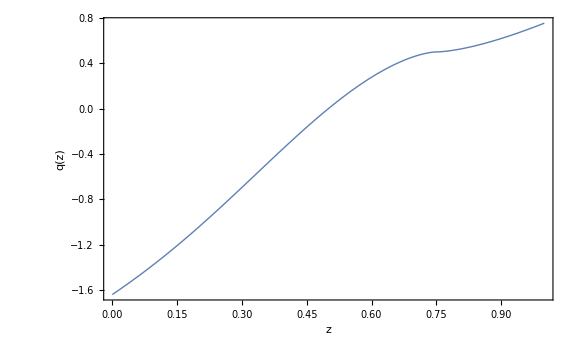

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-2.04019},{0.01,-1.97401},{0.02,-1.9085},{0.03,-1.84374},{0.04,-1.77977},{0.05,-1.71664},{0.06,-1.65438},{0.07,-1.59306},{0.08,-1.53268},{0.09,-1.4733},{0.1,-1.41493},{0.11,-1.3576},{0.12,-1.30134},{0.13,-1.24616},{0.14,-1.19207},{0.15,-1.13909},{0.16,-1.08723},{0.17,-1.03649},{0.18,-0.986904},{0.19,-0.938422},{0.2,-0.891074},{0.21,-0.844884},{0.22,-0.799802},{0.23,-0.755831},{0.24,-0.712989},{0.25,-0.671268},{0.26,-0.63062},{0.27,-0.591056},{0.28,-0.552582},{0.29,-0.515172},{0.3,-0.478789},{0.31,-0.443437},{0.32,-0.409115},{0.33,-0.375797},{0.34,-0.343444},{0.35,-0.312053},{0.36,-0.281617},{0.37,-0.252122},{0.38,-0.223523},{0.39,-0.195808},{0.4,-0.168968},{0.41,-0.142992},{0.42,-0.117851},{0.43,-0.0935136},{0.44,-0.0699679},{0.45,-0.0472019},{0.46,-0.025202},{0.47,-0.00393661},{0.48,0.0166152},{0.49,0.0364667},{0.5,0.0556321},{0.51,0.0741321},{0.52,0.0919914},{0.53,0.109224},{0.54,0.125845},{0.55,0.141869},{0.56,0.15732},{0.57,0.172214},{0.58,0.186565},{0.59,0.200388},{0.6,0.213698},{0.61,0.226515},{0.62,0.238853},{0.63,0.250724},{0.64,0.262143},{0.65,0.273126},{0.66,0.283685},{0.67,0.293835},{0.68,0.303588},{0.69,0.312958},{0.7,0.321956},{0.71,0.330595},{0.72,0.338887},{0.73,0.346842},{0.74,0.354474},{0.75,0.361792},{0.76,0.368807},{0.77,0.375528},{0.78,0.381967},{0.79,0.388134},{0.8,0.394038},{0.81,0.399686},{0.82,0.405088},{0.83,0.410254},{0.84,0.415193},{0.85,0.419914},{0.86,0.424419},{0.87,0.428719},{0.88,0.432822},{0.89,0.436737},{0.9,0.440471},{0.91,0.444026},{0.92,0.447412},{0.93,0.450635},{0.94,0.453702},{0.95,0.456617},{0.96,0.459386},{0.97,0.462017},{0.98,0.464513},{0.99,0.46688},{1.,0.469124}}

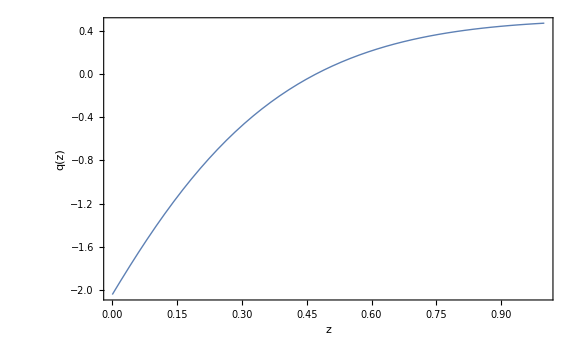

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-2.84284},{0.01,-2.66722},{0.02,-2.50058},{0.03,-2.34263},{0.04,-2.19308},{0.05,-2.0516},{0.06,-1.91783},{0.07,-1.79147},{0.08,-1.67214},{0.09,-1.55952},{0.1,-1.45326},{0.11,-1.35304},{0.12,-1.25852},{0.13,-1.16939},{0.14,-1.08535},{0.15,-1.00612},{0.16,-0.93143},{0.17,-0.860976},{0.18,-0.794561},{0.19,-0.731904},{0.2,-0.672802},{0.21,-0.617036},{0.22,-0.564397},{0.23,-0.514712},{0.24,-0.467782},{0.25,-0.423459},{0.26,-0.381568},{0.27,-0.341976},{0.28,-0.304532},{0.29,-0.269113},{0.3,-0.235597},{0.31,-0.203857},{0.32,-0.173811},{0.33,-0.145333},{0.34,-0.118338},{0.35,-0.0927502},{0.36,-0.0684661},{0.37,-0.0454211},{0.38,-0.0235467},{0.39,-0.00276122},{0.4,0.0169885},{0.41,0.0357596},{0.42,0.0536185},{0.43,0.07061},{0.44,0.0867797},{0.45,0.102183},{0.46,0.116857},{0.47,0.13084},{0.48,0.144174},{0.49,0.156895},{0.5,0.169033},{0.51,0.180619},{0.52,0.191687},{0.53,0.202262},{0.54,0.212367},{0.55,0.222029},{0.56,0.231275},{0.57,0.240124},{0.58,0.248594},{0.59,0.256704},{0.6,0.264471},{0.61,0.271916},{0.62,0.279057},{0.63,0.285906},{0.64,0.292477},{0.65,0.298782},{0.66,0.304834},{0.67,0.310647},{0.68,0.316233},{0.69,0.321604},{0.7,0.326767},{0.71,0.331733},{0.72,0.336509},{0.73,0.341104},{0.74,0.345528},{0.75,0.349789},{0.76,0.353895},{0.77,0.357852},{0.78,0.361665},{0.79,0.365341},{0.8,0.368886},{0.81,0.372305},{0.82,0.375605},{0.83,0.378792},{0.84,0.38187},{0.85,0.384842},{0.86,0.387714},{0.87,0.390489},{0.88,0.39317},{0.89,0.395762},{0.9,0.39827},{0.91,0.400697},{0.92,0.403045},{0.93,0.405318},{0.94,0.407518},{0.95,0.409648},{0.96,0.411712},{0.97,0.413712},{0.98,0.41565},{0.99,0.417529},{1.,0.41935}}

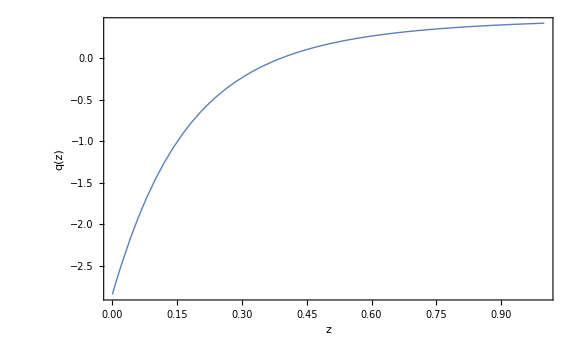

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-3.24417},{0.01,-2.99995},{0.02,-2.77281},{0.03,-2.56169},{0.04,-2.36559},{0.05,-2.18349},{0.06,-2.01443},{0.07,-1.85751},{0.08,-1.71187},{0.09,-1.57667},{0.1,-1.45113},{0.11,-1.33454},{0.12,-1.22624},{0.13,-1.12557},{0.14,-1.03195},{0.15,-0.944882},{0.16,-0.863842},{0.17,-0.788356},{0.18,-0.718004},{0.19,-0.652416},{0.2,-0.591212},{0.21,-0.534052},{0.22,-0.480658},{0.23,-0.430721},{0.24,-0.384001},{0.25,-0.340253},{0.26,-0.299256},{0.27,-0.260817},{0.28,-0.224741},{0.29,-0.190867},{0.3,-0.159029},{0.31,-0.129091},{0.32,-0.100915},{0.33,-0.074379},{0.34,-0.0493731},{0.35,-0.0257862},{0.36,-0.00353173},{0.37,0.017491},{0.38,0.0373494},{0.39,0.0561361},{0.4,0.0739169},{0.41,0.0907448},{0.42,0.106688},{0.43,0.121812},{0.44,0.136159},{0.45,0.14977},{0.46,0.162703},{0.47,0.174999},{0.48,0.186689},{0.49,0.197808},{0.5,0.208398},{0.51,0.218489},{0.52,0.228105},{0.53,0.237271},{0.54,0.246019},{0.55,0.254374},{0.56,0.262353},{0.57,0.269975},{0.58,0.277263},{0.59,0.284237},{0.6,0.290913},{0.61,0.297303},{0.62,0.303422},{0.63,0.309289},{0.64,0.314916},{0.65,0.320314},{0.66,0.325493},{0.67,0.330463},{0.68,0.33524},{0.69,0.339831},{0.7,0.344245},{0.71,0.348488},{0.72,0.352569},{0.73,0.356498},{0.74,0.360283},{0.75,0.363929},{0.76,0.367441},{0.77,0.370825},{0.78,0.374083},{0.79,0.377231},{0.8,0.380271},{0.81,0.383208},{0.82,0.386045},{0.83,0.388786},{0.84,0.391433},{0.85,0.39399},{0.86,0.396461},{0.87,0.398847},{0.88,0.401157},{0.89,0.403396},{0.9,0.405564},{0.91,0.407665},{0.92,0.409699},{0.93,0.411669},{0.94,0.413577},{0.95,0.415429},{0.96,0.417226},{0.97,0.418969},{0.98,0.420661},{0.99,0.422302},{1.,0.423894}}

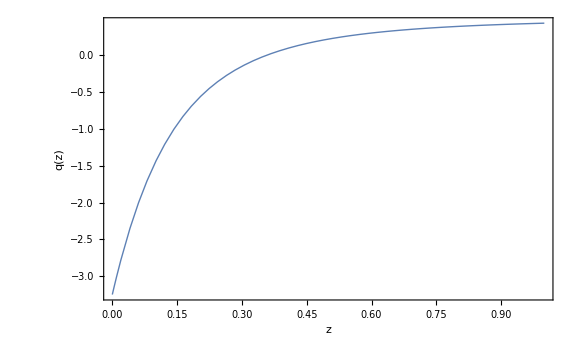

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

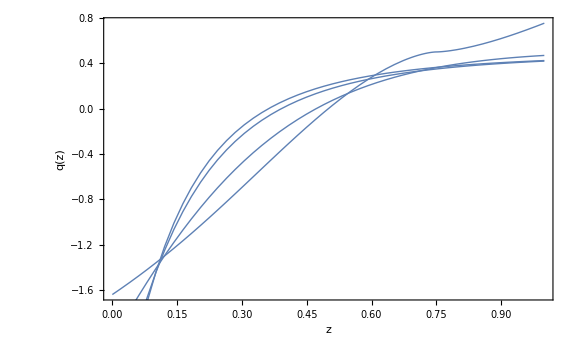

```mathematica
Show[p04n, p02n, p02, p04]
```

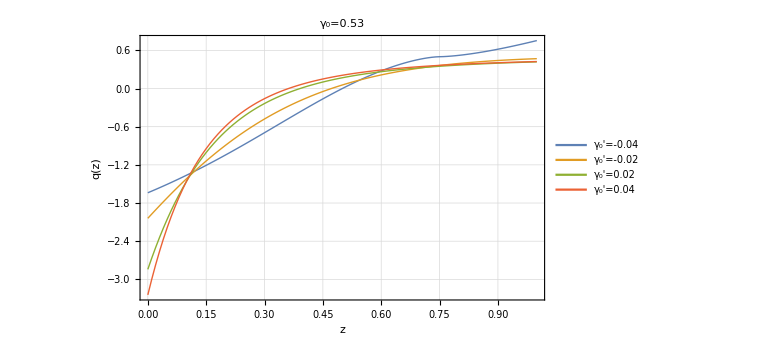

```mathematica
list=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0'=-0.04", "γ_0'=-0.02", "γ_0'=0.02", "γ_0'=0.04"},LegendFunction->"Frame", Background->White],{Right,Bottom}], GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["γ_0=0.53", Black, FontSize->20]]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.450033},{0.01,-0.446444},{0.02,-0.442969},{0.03,-0.439596},{0.04,-0.436322},{0.05,-0.433142},{0.06,-0.430055},{0.07,-0.427056},{0.08,-0.42414},{0.09,-0.421304},{0.1,-0.418542},{0.11,-0.415857},{0.12,-0.413234},{0.13,-0.410683},{0.14,-0.408186},{0.15,-0.405754},{0.16,-0.403368},{0.17,-0.40104},{0.18,-0.398754},{0.19,-0.396513},{0.2,-0.394314},{0.21,-0.392145},{0.22,-0.390017},{0.23,-0.387906},{0.24,-0.385832},{0.25,-0.383787},{0.26,-0.381745},{0.27,-0.379717},{0.28,-0.377719},{0.29,-0.375725},{0.3,-0.373716},{0.31,-0.371725},{0.32,-0.369742},{0.33,-0.367742},{0.34,-0.365717},{0.35,-0.3637},{0.36,-0.361673},{0.37,-0.359615},{0.38,-0.357519},{0.39,-0.355414},{0.4,-0.353285},{0.41,-0.351115},{0.42,-0.348895},{0.43,-0.346641},{0.44,-0.344341},{0.45,-0.341991},{0.46,-0.339588},{0.47,-0.337128},{0.48,-0.334606},{0.49,-0.332019},{0.5,-0.329361},{0.51,-0.326631},{0.52,-0.323821},{0.53,-0.320932},{0.54,-0.317955},{0.55,-0.314888},{0.56,-0.311727},{0.57,-0.308466},{0.58,-0.305102},{0.59,-0.301629},{0.6,-0.298045},{0.61,-0.294344},{0.62,-0.290521},{0.63,-0.286571},{0.64,-0.282491},{0.65,-0.278275},{0.66,-0.273918},{0.67,-0.269417},{0.68,-0.264765},{0.69,-0.259958},{0.7,-0.254991},{0.71,-0.249857},{0.72,-0.244555},{0.73,-0.239076},{0.74,-0.233417},{0.75,-0.227572},{0.76,-0.221535},{0.77,-0.215302},{0.78,-0.208867},{0.79,-0.202224},{0.8,-0.195366},{0.81,-0.188292},{0.82,-0.180993},{0.83,-0.173461},{0.84,-0.165697},{0.85,-0.157687},{0.86,-0.149432},{0.87,-0.140922},{0.88,-0.13215},{0.89,-0.123116},{0.9,-0.113803},{0.91,-0.104217},{0.92,-0.0943382},{0.93,-0.0841736},{0.94,-0.0737025},{0.95,-0.0629307},{0.96,-0.0518393},{0.97,-0.0404302},{0.98,-0.0286884},{0.99,-0.01661},{1.,-0.00418454}}

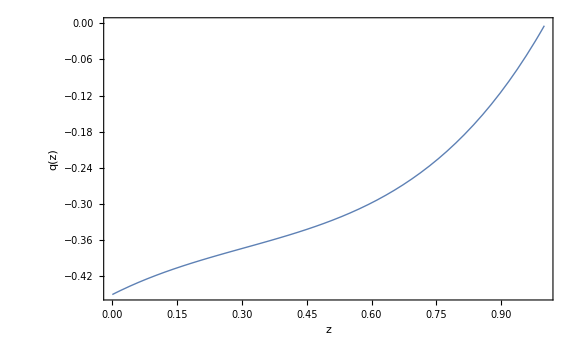

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.690827},{0.01,-0.675469},{0.02,-0.660393},{0.03,-0.645588},{0.04,-0.63105},{0.05,-0.616771},{0.06,-0.602746},{0.07,-0.588968},{0.08,-0.57543},{0.09,-0.562127},{0.1,-0.549052},{0.11,-0.536201},{0.12,-0.523566},{0.13,-0.511144},{0.14,-0.498926},{0.15,-0.486913},{0.16,-0.475092},{0.17,-0.463464},{0.18,-0.452024},{0.19,-0.440762},{0.2,-0.429681},{0.21,-0.418771},{0.22,-0.408027},{0.23,-0.39745},{0.24,-0.387033},{0.25,-0.376768},{0.26,-0.36666},{0.27,-0.356699},{0.28,-0.346878},{0.29,-0.337204},{0.3,-0.327667},{0.31,-0.318259},{0.32,-0.308985},{0.33,-0.299842},{0.34,-0.290824},{0.35,-0.281921},{0.36,-0.273137},{0.37,-0.264476},{0.38,-0.255928},{0.39,-0.247487},{0.4,-0.239148},{0.41,-0.230921},{0.42,-0.222801},{0.43,-0.21478},{0.44,-0.206853},{0.45,-0.199017},{0.46,-0.191283},{0.47,-0.183643},{0.48,-0.176092},{0.49,-0.168625},{0.5,-0.161238},{0.51,-0.153942},{0.52,-0.146731},{0.53,-0.139601},{0.54,-0.132546},{0.55,-0.125564},{0.56,-0.118657},{0.57,-0.111829},{0.58,-0.105076},{0.59,-0.0983938},{0.6,-0.0917777},{0.61,-0.0852249},{0.62,-0.0787396},{0.63,-0.0723242},{0.64,-0.065975},{0.65,-0.0596888},{0.66,-0.0534623},{0.67,-0.0472929},{0.68,-0.0411833},{0.69,-0.0351337},{0.7,-0.0291416},{0.71,-0.0232052},{0.72,-0.0173245},{0.73,-0.0114977},{0.74,-0.00572448},{0.75,-3.35809×10^-6},{0.76,0.00566607},{0.77,0.0112849},{0.78,0.016854},{0.79,0.0223739},{0.8,0.0278461},{0.81,0.0332704},{0.82,0.0386477},{0.83,0.0439795},{0.84,0.049266},{0.85,0.0545075},{0.86,0.059705},{0.87,0.0648594},{0.88,0.0699709},{0.89,0.0750402},{0.9,0.0800681},{0.91,0.0850549},{0.92,0.0900012},{0.93,0.0949075},{0.94,0.0997745},{0.95,0.104602},{0.96,0.109392},{0.97,0.114143},{0.98,0.118857},{0.99,0.123534},{1.,0.128174}}

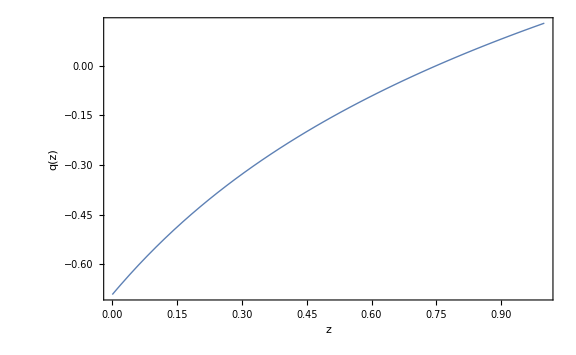

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.17242},{0.01,-1.12256},{0.02,-1.0745},{0.03,-1.02817},{0.04,-0.983509},{0.05,-0.940457},{0.06,-0.898955},{0.07,-0.858946},{0.08,-0.820366},{0.09,-0.783174},{0.1,-0.747302},{0.11,-0.712715},{0.12,-0.679348},{0.13,-0.647166},{0.14,-0.616112},{0.15,-0.586152},{0.16,-0.557235},{0.17,-0.529323},{0.18,-0.502379},{0.19,-0.476359},{0.2,-0.451239},{0.21,-0.426967},{0.22,-0.403511},{0.23,-0.380848},{0.24,-0.358957},{0.25,-0.337788},{0.26,-0.317314},{0.27,-0.297517},{0.28,-0.278374},{0.29,-0.259846},{0.3,-0.241914},{0.31,-0.224561},{0.32,-0.207767},{0.33,-0.191498},{0.34,-0.175738},{0.35,-0.160473},{0.36,-0.14569},{0.37,-0.131356},{0.38,-0.117457},{0.39,-0.103983},{0.4,-0.0909221},{0.41,-0.0782528},{0.42,-0.0659548},{0.43,-0.0540196},{0.44,-0.0424381},{0.45,-0.031201},{0.46,-0.0202856},{0.47,-0.00967957},{0.48,0.000623975},{0.49,0.0106319},{0.5,0.0203517},{0.51,0.0298027},{0.52,0.0389962},{0.53,0.0479373},{0.54,0.0566312},{0.55,0.0650835},{0.56,0.073305},{0.57,0.0813123},{0.58,0.0891093},{0.59,0.0967},{0.6,0.104088},{0.61,0.111278},{0.62,0.118284},{0.63,0.125114},{0.64,0.13177},{0.65,0.138256},{0.66,0.144575},{0.67,0.150735},{0.68,0.156746},{0.69,0.16261},{0.7,0.168331},{0.71,0.173908},{0.72,0.179347},{0.73,0.184659},{0.74,0.189848},{0.75,0.194915},{0.76,0.199861},{0.77,0.204687},{0.78,0.209399},{0.79,0.214006},{0.8,0.218511},{0.81,0.222914},{0.82,0.227216},{0.83,0.231419},{0.84,0.235524},{0.85,0.239542},{0.86,0.243475},{0.87,0.247321},{0.88,0.251083},{0.89,0.25476},{0.9,0.258359},{0.91,0.261884},{0.92,0.265335},{0.93,0.268714},{0.94,0.272019},{0.95,0.275253},{0.96,0.278424},{0.97,0.281532},{0.98,0.284576},{0.99,0.287558},{1.,0.290477}}

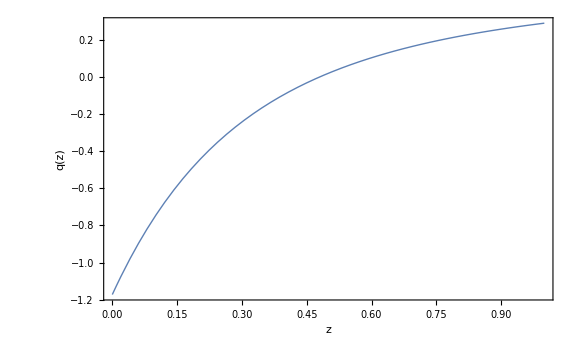

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.41321},{0.01,-1.34076},{0.02,-1.27167},{0.03,-1.20579},{0.04,-1.14295},{0.05,-1.08302},{0.06,-1.02583},{0.07,-0.971256},{0.08,-0.919175},{0.09,-0.869452},{0.1,-0.821964},{0.11,-0.776608},{0.12,-0.733273},{0.13,-0.691851},{0.14,-0.652256},{0.15,-0.614379},{0.16,-0.578159},{0.17,-0.543482},{0.18,-0.510298},{0.19,-0.478513},{0.2,-0.448064},{0.21,-0.418893},{0.22,-0.390919},{0.23,-0.364102},{0.24,-0.338372},{0.25,-0.313677},{0.26,-0.289979},{0.27,-0.267213},{0.28,-0.245343},{0.29,-0.224333},{0.3,-0.204126},{0.31,-0.184696},{0.32,-0.166026},{0.33,-0.148038},{0.34,-0.130706},{0.35,-0.114012},{0.36,-0.0979365},{0.37,-0.0824601},{0.38,-0.0675544},{0.39,-0.0531625},{0.4,-0.0392697},{0.41,-0.0258629},{0.42,-0.0129285},{0.43,-0.000451379},{0.44,0.0116093},{0.45,0.0232724},{0.46,0.0345472},{0.47,0.0454434},{0.48,0.0559706},{0.49,0.0661567},{0.5,0.0760228},{0.51,0.085575},{0.52,0.09482},{0.53,0.103767},{0.54,0.112443},{0.55,0.120855},{0.56,0.129009},{0.57,0.13691},{0.58,0.144569},{0.59,0.152008},{0.6,0.159231},{0.61,0.166241},{0.62,0.173042},{0.63,0.179642},{0.64,0.186062},{0.65,0.192305},{0.66,0.198373},{0.67,0.204267},{0.68,0.209992},{0.69,0.215567},{0.7,0.220996},{0.71,0.226278},{0.72,0.231415},{0.73,0.236413},{0.74,0.241286},{0.75,0.246036},{0.76,0.250662},{0.77,0.255165},{0.78,0.259551},{0.79,0.263834},{0.8,0.268013},{0.81,0.272088},{0.82,0.276059},{0.83,0.279928},{0.84,0.28371},{0.85,0.287405},{0.86,0.291014},{0.87,0.294535},{0.88,0.297969},{0.89,0.301322},{0.9,0.304605},{0.91,0.307816},{0.92,0.310954},{0.93,0.314018},{0.94,0.317009},{0.95,0.319937},{0.96,0.322805},{0.97,0.325612},{0.98,0.328357},{0.99,0.331038},{1.,0.333667}}

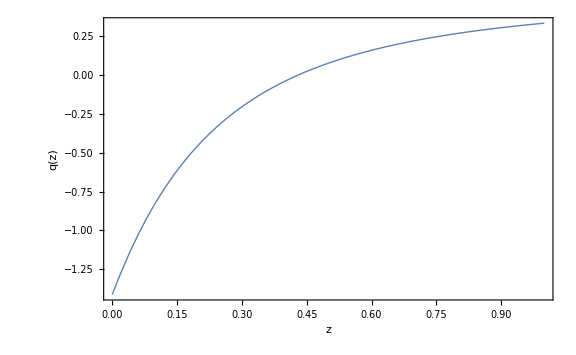

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

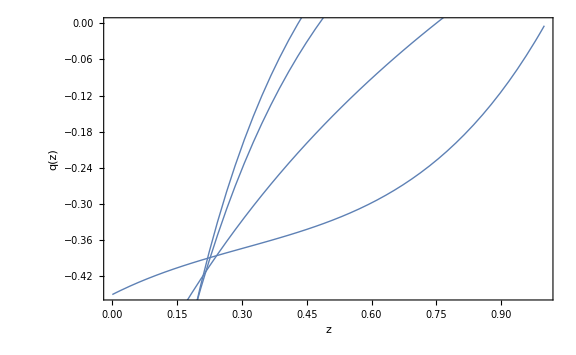

```mathematica
Show[p04n, p02n, p02, p04]
```

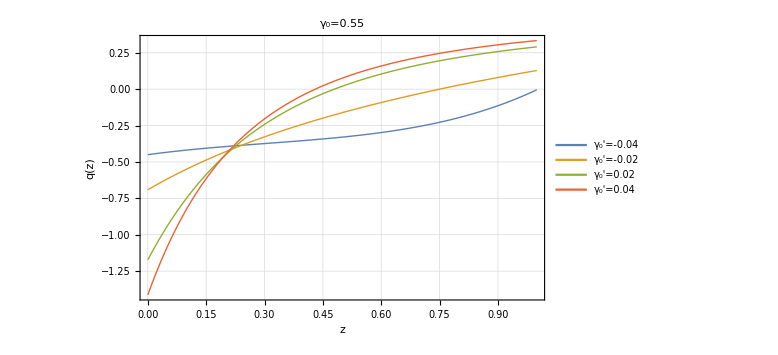

```mathematica
list2=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0'=-0.04", "γ_0'=-0.02", "γ_0'=0.02", "γ_0'=0.04"},LegendFunction->"Frame", Background->White],{Right,Bottom}], GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["γ_0=0.55", Black, FontSize->20]]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.57;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,0.0609468},{0.01,0.0606423},{0.02,0.0602828},{0.03,0.0598691},{0.04,0.0594022},{0.05,0.0588827},{0.06,0.0583114},{0.07,0.057689},{0.08,0.0570164},{0.09,0.0562939},{0.1,0.0555224},{0.11,0.0547026},{0.12,0.0538342},{0.13,0.0529198},{0.14,0.0519565},{0.15,0.0509496},{0.16,0.0498936},{0.17,0.0487953},{0.18,0.0476497},{0.19,0.0464593},{0.2,0.0452279},{0.21,0.0439477},{0.22,0.0426292},{0.23,0.0412643},{0.24,0.0398549},{0.25,0.0384097},{0.26,0.0369147},{0.27,0.0353799},{0.28,0.0338076},{0.29,0.0321878},{0.3,0.0305327},{0.31,0.028831},{0.32,0.0270912},{0.33,0.0253121},{0.34,0.0234876},{0.35,0.0216307},{0.36,0.0197262},{0.37,0.0177839},{0.38,0.0158067},{0.39,0.0137812},{0.4,0.011724},{0.41,0.0096254},{0.42,0.00748147},{0.43,0.00530839},{0.44,0.00308978},{0.45,0.000832712},{0.46,-0.00145891},{0.47,-0.00379634},{0.48,-0.00616379},{0.49,-0.00857678},{0.5,-0.0110275},{0.51,-0.01351},{0.52,-0.0160404},{0.53,-0.0186012},{0.54,-0.0212019},{0.55,-0.0238468},{0.56,-0.0265184},{0.57,-0.029236},{0.58,-0.0319941},{0.59,-0.0347775},{0.6,-0.0376096},{0.61,-0.0404805},{0.62,-0.0433772},{0.63,-0.0463216},{0.64,-0.0493},{0.65,-0.0523123},{0.66,-0.0553695},{0.67,-0.0584537},{0.68,-0.0615818},{0.69,-0.064748},{0.7,-0.0679408},{0.71,-0.0711812},{0.72,-0.0744541},{0.73,-0.0777564},{0.74,-0.0811061},{0.75,-0.0844845},{0.76,-0.0878948},{0.77,-0.0913515},{0.78,-0.094835},{0.79,-0.0983501},{0.8,-0.101911},{0.81,-0.1055},{0.82,-0.109115},{0.83,-0.112778},{0.84,-0.11647},{0.85,-0.120183},{0.86,-0.123943},{0.87,-0.127735},{0.88,-0.131545},{0.89,-0.135397},{0.9,-0.13928},{0.91,-0.143183},{0.92,-0.147126},{0.93,-0.151097},{0.94,-0.155086},{0.95,-0.159113},{0.96,-0.163166},{0.97,-0.167237},{0.98,-0.171339},{0.99,-0.175462},{1.,-0.17961}}

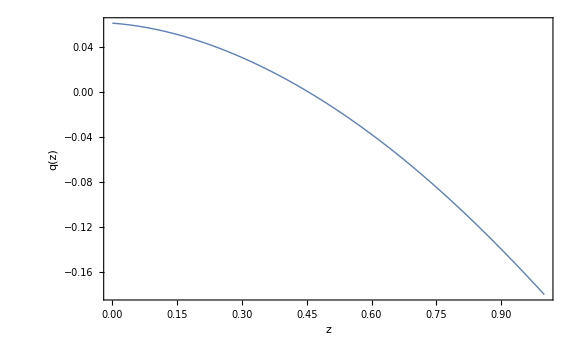

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.111049},{0.01,-0.106778},{0.02,-0.102601},{0.03,-0.098523},{0.04,-0.0945398},{0.05,-0.0906482},{0.06,-0.0868447},{0.07,-0.0831272},{0.08,-0.0794938},{0.09,-0.0759415},{0.1,-0.0724678},{0.11,-0.0690722},{0.12,-0.0657484},{0.13,-0.0624987},{0.14,-0.059321},{0.15,-0.0562089},{0.16,-0.0531643},{0.17,-0.0501866},{0.18,-0.0472695},{0.19,-0.0444137},{0.2,-0.0416198},{0.21,-0.0388827},{0.22,-0.0362012},{0.23,-0.0335759},{0.24,-0.031005},{0.25,-0.0284851},{0.26,-0.026016},{0.27,-0.0235971},{0.28,-0.0212265},{0.29,-0.0189026},{0.3,-0.0166247},{0.31,-0.0143915},{0.32,-0.012202},{0.33,-0.0100549},{0.34,-0.0079487},{0.35,-0.00588335},{0.36,-0.00385767},{0.37,-0.00186986},{0.38,0.0000812357},{0.39,0.00199462},{0.4,0.00387216},{0.41,0.00571602},{0.42,0.00752655},{0.43,0.0093026},{0.44,0.0110466},{0.45,0.0127606},{0.46,0.0144424},{0.47,0.0160939},{0.48,0.0177177},{0.49,0.019313},{0.5,0.0208788},{0.51,0.0224178},{0.52,0.0239326},{0.53,0.0254198},{0.54,0.0268804},{0.55,0.0283177},{0.56,0.0297332},{0.57,0.0311226},{0.58,0.032488},{0.59,0.0338326},{0.6,0.0351576},{0.61,0.0364587},{0.62,0.0377385},{0.63,0.0390003},{0.64,0.0402417},{0.65,0.0414619},{0.66,0.0426644},{0.67,0.0438509},{0.68,0.0450168},{0.69,0.0461643},{0.7,0.047297},{0.71,0.0484144},{0.72,0.0495124},{0.73,0.0505944},{0.74,0.0516637},{0.75,0.0527186},{0.76,0.0537556},{0.77,0.0547781},{0.78,0.0557896},{0.79,0.0567889},{0.8,0.0577711},{0.81,0.0587399},{0.82,0.0596985},{0.83,0.0606474},{0.84,0.061581},{0.85,0.0625024},{0.86,0.0634151},{0.87,0.0643173},{0.88,0.0652061},{0.89,0.066085},{0.9,0.0669571},{0.91,0.067818},{0.92,0.0686671},{0.93,0.069508},{0.94,0.0703429},{0.95,0.0711672},{0.96,0.0719822},{0.97,0.0727913},{0.98,0.0735915},{0.99,0.0743831},{1.,0.0751692}}

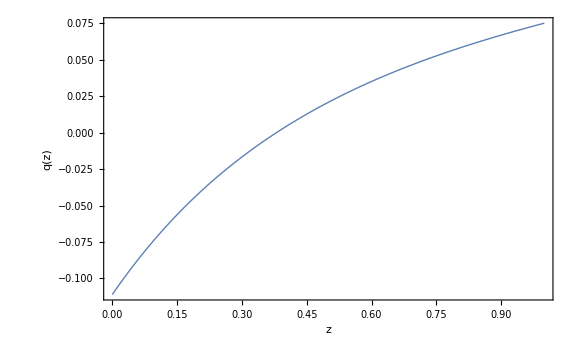

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.455042},{0.01,-0.435899},{0.02,-0.417302},{0.03,-0.399239},{0.04,-0.381688},{0.05,-0.364633},{0.06,-0.348055},{0.07,-0.331939},{0.08,-0.316269},{0.09,-0.301028},{0.1,-0.286204},{0.11,-0.271782},{0.12,-0.257747},{0.13,-0.244088},{0.14,-0.230792},{0.15,-0.217844},{0.16,-0.205239},{0.17,-0.192956},{0.18,-0.180996},{0.19,-0.169337},{0.2,-0.157975},{0.21,-0.146904},{0.22,-0.136104},{0.23,-0.12558},{0.24,-0.115311},{0.25,-0.105292},{0.26,-0.0955249},{0.27,-0.0859852},{0.28,-0.0766739},{0.29,-0.0675942},{0.3,-0.0587211},{0.31,-0.0500527},{0.32,-0.0415946},{0.33,-0.0333316},{0.34,-0.0252496},{0.35,-0.0173552},{0.36,-0.00964876},{0.37,-0.00210548},{0.38,0.00527326},{0.39,0.0124815},{0.4,0.019526},{0.41,0.0264282},{0.42,0.0331824},{0.43,0.0397828},{0.44,0.0462386},{0.45,0.0525692},{0.46,0.0587682},{0.47,0.06483},{0.48,0.0707591},{0.49,0.0765781},{0.5,0.0822823},{0.51,0.0878656},{0.52,0.0933248},{0.53,0.0986828},{0.54,0.103943},{0.55,0.109099},{0.56,0.114145},{0.57,0.119085},{0.58,0.123942},{0.59,0.128712},{0.6,0.133389},{0.61,0.137969},{0.62,0.142458},{0.63,0.146873},{0.64,0.151211},{0.65,0.155464},{0.66,0.159631},{0.67,0.163728},{0.68,0.167759},{0.69,0.171716},{0.7,0.175596},{0.71,0.179402},{0.72,0.183151},{0.73,0.186839},{0.74,0.190461},{0.75,0.194013},{0.76,0.1975},{0.77,0.200939},{0.78,0.204324},{0.79,0.20765},{0.8,0.210913},{0.81,0.214116},{0.82,0.217276},{0.83,0.220391},{0.84,0.223455},{0.85,0.226464},{0.86,0.229416},{0.87,0.232328},{0.88,0.235199},{0.89,0.238026},{0.9,0.240805},{0.91,0.243534},{0.92,0.246228},{0.93,0.248884},{0.94,0.251499},{0.95,0.25407},{0.96,0.256598},{0.97,0.259097},{0.98,0.261561},{0.99,0.263986},{1.,0.26637}}

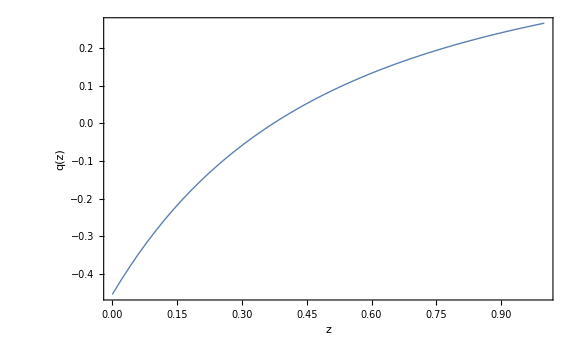

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.627038},{0.01,-0.597651},{0.02,-0.569307},{0.03,-0.541966},{0.04,-0.515586},{0.05,-0.490123},{0.06,-0.465542},{0.07,-0.441807},{0.08,-0.418878},{0.09,-0.396729},{0.1,-0.37532},{0.11,-0.35463},{0.12,-0.334618},{0.13,-0.31527},{0.14,-0.296544},{0.15,-0.27843},{0.16,-0.26089},{0.17,-0.24391},{0.18,-0.227466},{0.19,-0.211532},{0.2,-0.196099},{0.21,-0.181131},{0.22,-0.166626},{0.23,-0.152559},{0.24,-0.138906},{0.25,-0.125668},{0.26,-0.112818},{0.27,-0.100336},{0.28,-0.0882226},{0.29,-0.0764602},{0.3,-0.0650215},{0.31,-0.0539101},{0.32,-0.0431198},{0.33,-0.0326161},{0.34,-0.0224},{0.35,-0.012475},{0.36,-0.00281402},{0.37,0.00659761},{0.38,0.0157544},{0.39,0.0246572},{0.4,0.0333395},{0.41,0.0418026},{0.42,0.0500411},{0.43,0.0580583},{0.44,0.065887},{0.45,0.0735249},{0.46,0.0809659},{0.47,0.0882108},{0.48,0.0952918},{0.49,0.102209},{0.5,0.108956},{0.51,0.115527},{0.52,0.121949},{0.53,0.128232},{0.54,0.134371},{0.55,0.140359},{0.56,0.146201},{0.57,0.151923},{0.58,0.157521},{0.59,0.162989},{0.6,0.168326},{0.61,0.173556},{0.62,0.178679},{0.63,0.183687},{0.64,0.188576},{0.65,0.193368},{0.66,0.198068},{0.67,0.202669},{0.68,0.207166},{0.69,0.211564},{0.7,0.215886},{0.71,0.220125},{0.72,0.224275},{0.73,0.22833},{0.74,0.232307},{0.75,0.236217},{0.76,0.240055},{0.77,0.243815},{0.78,0.24749},{0.79,0.2511},{0.8,0.254651},{0.81,0.258137},{0.82,0.261551},{0.83,0.264896},{0.84,0.268189},{0.85,0.271428},{0.86,0.274605},{0.87,0.277716},{0.88,0.280774},{0.89,0.283787},{0.9,0.286749},{0.91,0.289656},{0.92,0.292504},{0.93,0.29531},{0.94,0.298074},{0.95,0.300789},{0.96,0.303452},{0.97,0.306075},{0.98,0.30866},{0.99,0.311202},{1.,0.313696}}

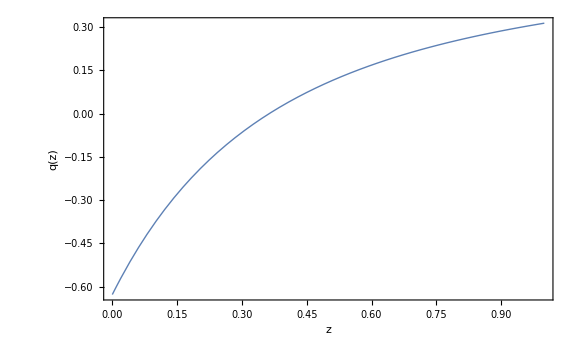

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

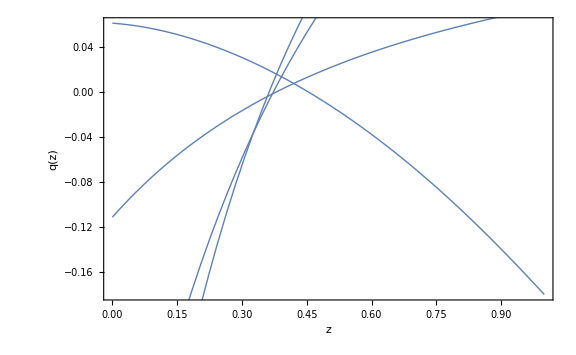

```mathematica
Show[p04n, p02n, p02, p04]
```

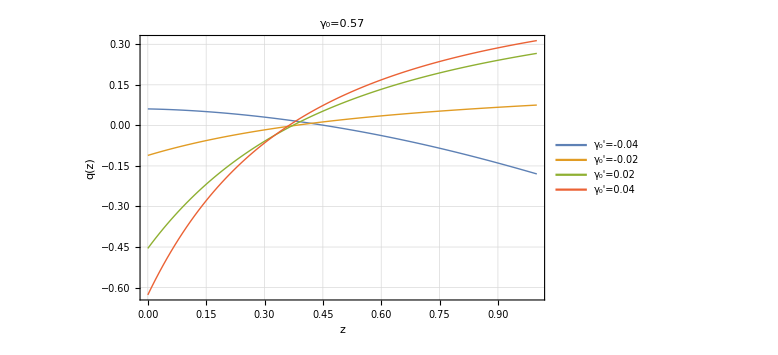

```mathematica
list3=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0'=-0.04", "γ_0'=-0.02", "γ_0'=0.02", "γ_0'=0.04"},LegendFunction->"Frame", Background->White],{Right,Bottom}], GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["γ_0=0.57", Black, FontSize->20]]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.59;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,0.346082},{0.01,0.345077},{0.02,0.344055},{0.03,0.343014},{0.04,0.341958},{0.05,0.340883},{0.06,0.339792},{0.07,0.33868},{0.08,0.337557},{0.09,0.336408},{0.1,0.33525},{0.11,0.334066},{0.12,0.332872},{0.13,0.331652},{0.14,0.330423},{0.15,0.329166},{0.16,0.327901},{0.17,0.326607},{0.18,0.325305},{0.19,0.323976},{0.2,0.322627},{0.21,0.321276},{0.22,0.319896},{0.23,0.318481},{0.24,0.317067},{0.25,0.315638},{0.26,0.314173},{0.27,0.312685},{0.28,0.311196},{0.29,0.309685},{0.3,0.308139},{0.31,0.306573},{0.32,0.305002},{0.33,0.303409},{0.34,0.301783},{0.35,0.300135},{0.36,0.298477},{0.37,0.296796},{0.38,0.295083},{0.39,0.293354},{0.4,0.291607},{0.41,0.289836},{0.42,0.288035},{0.43,0.286216},{0.44,0.284377},{0.45,0.282513},{0.46,0.28062},{0.47,0.278706},{0.48,0.27677},{0.49,0.274807},{0.5,0.272819},{0.51,0.270806},{0.52,0.268769},{0.53,0.266704},{0.54,0.264614},{0.55,0.262497},{0.56,0.260353},{0.57,0.258182},{0.58,0.255984},{0.59,0.253757},{0.6,0.2515},{0.61,0.249218},{0.62,0.246906},{0.63,0.244563},{0.64,0.242189},{0.65,0.239789},{0.66,0.237355},{0.67,0.234888},{0.68,0.232391},{0.69,0.229867},{0.7,0.227304},{0.71,0.224706},{0.72,0.222079},{0.73,0.219423},{0.74,0.216724},{0.75,0.213987},{0.76,0.21122},{0.77,0.208424},{0.78,0.205582},{0.79,0.202698},{0.8,0.19978},{0.81,0.196834},{0.82,0.19384},{0.83,0.190802},{0.84,0.187728},{0.85,0.18462},{0.86,0.18146},{0.87,0.178255},{0.88,0.175017},{0.89,0.171737},{0.9,0.1684},{0.91,0.165019},{0.92,0.161603},{0.93,0.158138},{0.94,0.154614},{0.95,0.151043},{0.96,0.147436},{0.97,0.143775},{0.98,0.140051},{0.99,0.136275},{1.,0.13246}}

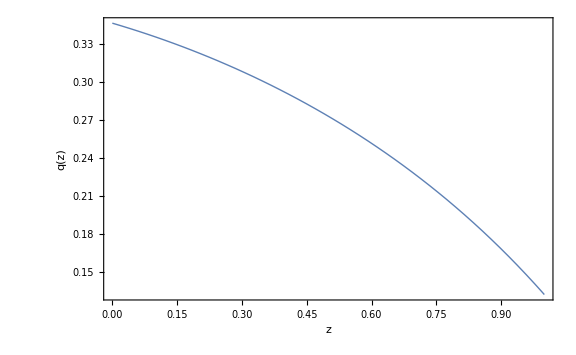

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,0.212307},{0.01,0.213199},{0.02,0.214061},{0.03,0.214892},{0.04,0.215694},{0.05,0.216468},{0.06,0.217214},{0.07,0.217932},{0.08,0.218628},{0.09,0.219292},{0.1,0.219937},{0.11,0.220552},{0.12,0.221149},{0.13,0.221716},{0.14,0.222267},{0.15,0.22279},{0.16,0.223295},{0.17,0.223778},{0.18,0.224238},{0.19,0.224683},{0.2,0.225095},{0.21,0.225504},{0.22,0.225891},{0.23,0.226243},{0.24,0.226594},{0.25,0.226929},{0.26,0.227228},{0.27,0.227521},{0.28,0.227805},{0.29,0.228063},{0.3,0.228295},{0.31,0.228528},{0.32,0.228747},{0.33,0.228934},{0.34,0.229109},{0.35,0.229283},{0.36,0.229439},{0.37,0.229565},{0.38,0.229684},{0.39,0.229801},{0.4,0.229902},{0.41,0.229974},{0.42,0.230036},{0.43,0.230098},{0.44,0.230148},{0.45,0.230176},{0.46,0.230172},{0.47,0.230175},{0.48,0.230181},{0.49,0.230178},{0.5,0.230157},{0.51,0.23011},{0.52,0.230032},{0.53,0.229958},{0.54,0.229889},{0.55,0.229817},{0.56,0.229734},{0.57,0.229632},{0.58,0.229505},{0.59,0.229353},{0.6,0.229206},{0.61,0.229064},{0.62,0.228918},{0.63,0.228763},{0.64,0.228593},{0.65,0.228404},{0.66,0.22819},{0.67,0.227983},{0.68,0.227767},{0.69,0.227544},{0.7,0.22731},{0.71,0.227067},{0.72,0.226816},{0.73,0.226556},{0.74,0.226287},{0.75,0.226011},{0.76,0.225724},{0.77,0.22543},{0.78,0.225129},{0.79,0.224817},{0.8,0.224498},{0.81,0.224173},{0.82,0.223838},{0.83,0.223495},{0.84,0.223145},{0.85,0.222787},{0.86,0.222419},{0.87,0.222047},{0.88,0.221668},{0.89,0.22128},{0.9,0.220882},{0.91,0.220478},{0.92,0.220069},{0.93,0.219653},{0.94,0.219228},{0.95,0.218795},{0.96,0.218357},{0.97,0.217911},{0.98,0.217458},{0.99,0.216998},{1.,0.216532}}

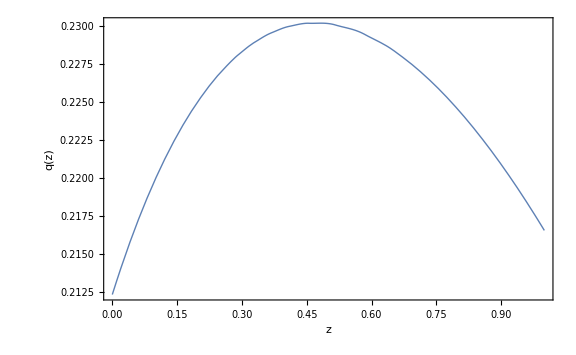

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.0552424},{0.01,-0.0470589},{0.02,-0.0390694},{0.03,-0.0312677},{0.04,-0.0236481},{0.05,-0.0162038},{0.06,-0.00892997},{0.07,-0.00182094},{0.08,0.0051274},{0.09,0.0119244},{0.1,0.0185673},{0.11,0.025069},{0.12,0.0314272},{0.13,0.0376512},{0.14,0.0437407},{0.15,0.0497047},{0.16,0.0555403},{0.17,0.0612604},{0.18,0.0668563},{0.19,0.0723467},{0.2,0.0777149},{0.21,0.0829888},{0.22,0.0881543},{0.23,0.0932085},{0.24,0.0981798},{0.25,0.103047},{0.26,0.107815},{0.27,0.112508},{0.28,0.117103},{0.29,0.121605},{0.3,0.126041},{0.31,0.130389},{0.32,0.134644},{0.33,0.138841},{0.34,0.142962},{0.35,0.146993},{0.36,0.150965},{0.37,0.154876},{0.38,0.158708},{0.39,0.162465},{0.4,0.166177},{0.41,0.169827},{0.42,0.173397},{0.43,0.176913},{0.44,0.180386},{0.45,0.183799},{0.46,0.187137},{0.47,0.19043},{0.48,0.193685},{0.49,0.196886},{0.5,0.200017},{0.51,0.203103},{0.52,0.206158},{0.53,0.209167},{0.54,0.212117},{0.55,0.215009},{0.56,0.217878},{0.57,0.220713},{0.58,0.223499},{0.59,0.226226},{0.6,0.22892},{0.61,0.231589},{0.62,0.234217},{0.63,0.236793},{0.64,0.239337},{0.65,0.241857},{0.66,0.244341},{0.67,0.246778},{0.68,0.249179},{0.69,0.251562},{0.7,0.253915},{0.71,0.256228},{0.72,0.258497},{0.73,0.26075},{0.74,0.262981},{0.75,0.265181},{0.76,0.267338},{0.77,0.269464},{0.78,0.271578},{0.79,0.273671},{0.8,0.275732},{0.81,0.277752},{0.82,0.279747},{0.83,0.281734},{0.84,0.283701},{0.85,0.285638},{0.86,0.287539},{0.87,0.289416},{0.88,0.291283},{0.89,0.293132},{0.9,0.294952},{0.91,0.29674},{0.92,0.298517},{0.93,0.30028},{0.94,0.302022},{0.95,0.303735},{0.96,0.305423},{0.97,0.307104},{0.98,0.308771},{0.99,0.310416},{1.,0.312031}}

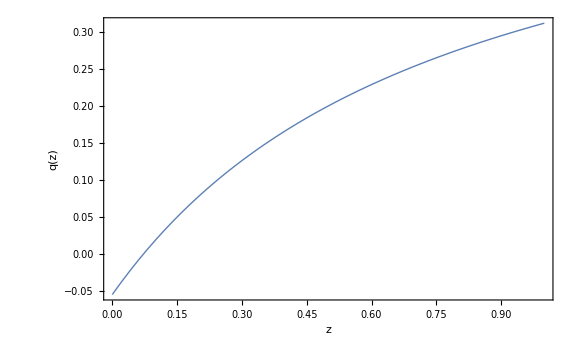

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.189017},{0.01,-0.175462},{0.02,-0.162296},{0.03,-0.149502},{0.04,-0.13707},{0.05,-0.124983},{0.06,-0.11323},{0.07,-0.101799},{0.08,-0.0906797},{0.09,-0.0798542},{0.1,-0.0693237},{0.11,-0.0590645},{0.12,-0.049079},{0.13,-0.0393469},{0.14,-0.0298701},{0.15,-0.0206284},{0.16,-0.0116263},{0.17,-0.0028414},{0.18,0.00571742},{0.19,0.0140759},{0.2,0.0222199},{0.21,0.030179},{0.22,0.037947},{0.23,0.0455192},{0.24,0.05293},{0.25,0.0601617},{0.26,0.0672194},{0.27,0.0741317},{0.28,0.0808787},{0.29,0.0874678},{0.3,0.0939268},{0.31,0.100236},{0.32,0.106396},{0.33,0.112442},{0.34,0.118355},{0.35,0.124125},{0.36,0.12979},{0.37,0.135342},{0.38,0.140762},{0.39,0.146072},{0.4,0.151291},{0.41,0.156399},{0.42,0.161386},{0.43,0.166291},{0.44,0.171108},{0.45,0.175822},{0.46,0.180427},{0.47,0.184965},{0.48,0.189424},{0.49,0.193788},{0.5,0.198052},{0.51,0.202258},{0.52,0.206396},{0.53,0.210451},{0.54,0.214411},{0.55,0.218314},{0.56,0.222162},{0.57,0.225942},{0.58,0.229638},{0.59,0.233266},{0.6,0.236848},{0.61,0.240372},{0.62,0.243822},{0.63,0.247212},{0.64,0.250561},{0.65,0.253855},{0.66,0.257082},{0.67,0.260253},{0.68,0.263389},{0.69,0.266477},{0.7,0.269505},{0.71,0.272473},{0.72,0.275413},{0.73,0.278314},{0.74,0.281164},{0.75,0.283953},{0.76,0.286708},{0.77,0.289436},{0.78,0.292124},{0.79,0.294762},{0.8,0.297345},{0.81,0.299907},{0.82,0.302443},{0.83,0.304941},{0.84,0.307392},{0.85,0.309797},{0.86,0.312184},{0.87,0.314544},{0.88,0.316866},{0.89,0.319143},{0.9,0.321398},{0.91,0.323631},{0.92,0.325834},{0.93,0.327996},{0.94,0.330129},{0.95,0.332243},{0.96,0.334328},{0.97,0.336379},{0.98,0.33841},{0.99,0.340418},{1.,0.342394}}

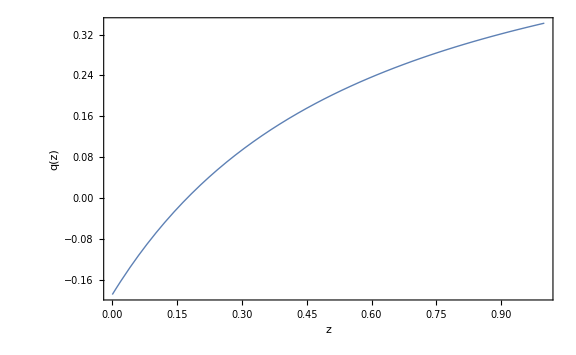

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

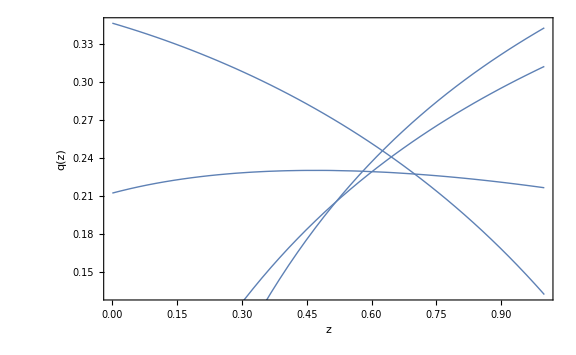

```mathematica
Show[p04n, p02n, p02, p04]
```

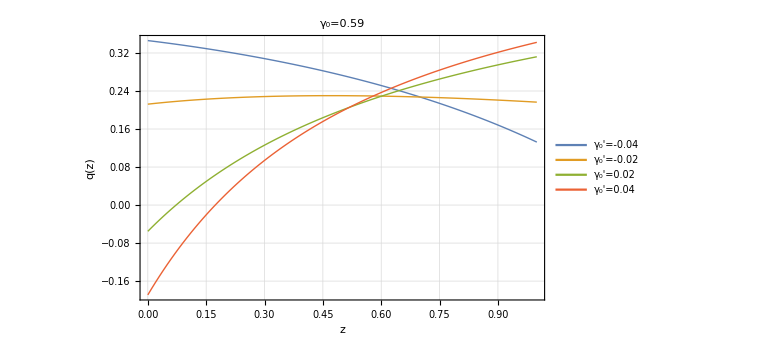

```mathematica
list4=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_0'=-0.04", "γ_0'=-0.02", "γ_0'=0.02", "γ_0'=0.04"},LegendFunction->"Frame", Background->White],{Right,Bottom}], GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["γ_0=0.59", Black, FontSize->20]]
```

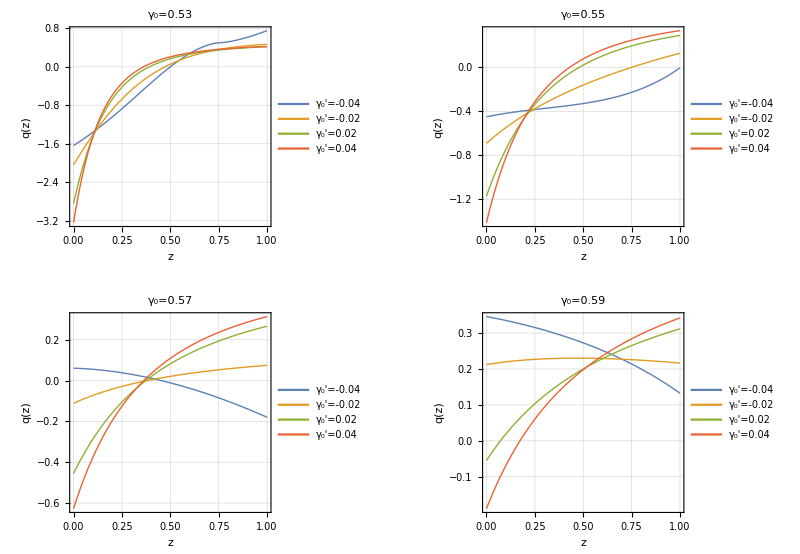

```mathematica
graph=GraphicsGrid[{{list,list2}, {list3, list4}}, ImageSize->Full]
```

```mathematica
SetDirectory["C:\\Users\\Gerald\\Desktop\\7sem\\dark energy\\final_plots"]
```

C:\Users\Gerald\Desktop\7sem\dark energy\final_plots

```mathematica
Export["q(z)_gamma0.png",graph,ImageResolution->700]
```

q(z)_gamma0.png